# Results

### Clear Stagnant Parameters

```mathematica
Clear[ele,Vo,uVo,F,R,kB,T,β,e,eo,NA,a,ao ,aoSI,aSI,aCond,l,lcgs,lsi,Lcgs,Lsi,σo,η,ηSI,ϵo,ϵDL,ϵSL]
```

```mathematica
Clear[QpH1,QpH2,QpH3,QpH4,QpH5,QpH6,QpH7,QpH8,QpH9,QpH10,QpH11,QpH12,QpH13,QpHi ]
```

```mathematica
Clear[λpH1 ,λpH2,λpH3,λpH4,λpH5,λpH6,λpH7,λpH8,λpH9,λpH10,λpH11,λpH12,λpH13,λpHi]
```

```mathematica
Clear[σpH1,σpH2,σpH3,σpH4,σpH5,σpH6,σpH7,σpH8,σpH9,σpH10,σpH11,σpH12,σpH13,σpHi,σoSI,σo]
```

## 1. Stagnant parameters

## Input Voltage

```mathematica
Vo=0.15
```

0.15

```mathematica
uVo=Quantity[Vo,"Volts"]
```

0.15 V

## Standard Constants

```mathematica
F=UnitConvert[Quantity["FaradayConstant"],"StatCoulombs"/"Moles"]
```

2.892558×10^14 statC/mol

```mathematica
(*R = = UnitConvert[UnitConvert[Quantity["GasConstant"],""],"Grams"*"Centimeters"^2/("Seconds"^2*"Kelvins"*"Moles")]*)
```

```mathematica
R = UnitConvert[UnitConvert[Quantity["GasConstant"],"SIBase"],"Grams"*"Centimeters"^2/("Seconds"^2*"Kelvins"*"Moles")]
```

8.3145×10^7 g cm^2/(s^2 K mol)

```mathematica
kB =UnitConvert[ Quantity["BoltzmannConstant"],"Ergs"/"Kelvins"]
```

1.3806×10^-16 ergs/K

```mathematica
T=Quantity[298.15,"Kelvins"]
```

298.15 K

```mathematica
β=1/kB/T
```

2.42931×10^13 per erg

```mathematica
e =UnitConvert[Quantity["ElementaryCharge"],"StatCoulombs"]
```

4.803205×10^-10 statC

```mathematica
eo=e
```

4.803205×10^-10 statC

```mathematica
NA =UnitConvert[Quantity["AvogadroConstant"],1/"Moles"]
```

6.022141×10^23 /mol

## Actin3

### radius

```mathematica
ao = UnitConvert[Quantity[(23.83)*10^(-10),"Meters"],"Centimeters"]
```

2.383×10^-7 cm

```mathematica
a = UnitConvert[Quantity[(23.83+0*2.5)*10^(-10),"Meters"],"Centimeters"]
```

2.383×10^-7 cm

```mathematica
aCond= a
```

2.383×10^-7 cm

```mathematica
aoSI = UnitConvert[ao,"SIBase"]
```

2.383×10^-9 m

```mathematica
aSI = UnitConvert[a,"SIBase"]
```

2.383×10^-9 m

### length

```mathematica
l=Quantity[5.4*10^-9,"Meters"]
```

5.4×10^-9 m

```mathematica
lsi=Quantity[5.4*10^-9,"Meters"]
```

5.4×10^-9 m

```mathematica
Lsi=Quantity[422.20*10^(-10),"Meters"]
```

4.222×10^-8 m

### Charge Q

```mathematica
(*Charge coming from tabulated values for Cong Model*)
QpH1 = 657*e;
QpH2=617*e;
QpH3=561*e;
QpH4=296*e;
QpH5=23*e;
QpH6=-82*e;
QpH7=-154*e;
QpH8=-184*e;
QpH9=-222*e;
QpH10=-269*e;
QpH11=-432*e;
QpH12=-476*e;
QpH13=-502*e;
```

```mathematica
QpHi = {QpH1,QpH2,QpH3,QpH4,QpH5,QpH6,QpH7,QpH8,QpH9,QpH10,QpH11,QpH12,QpH13}
```

{3.155705×10^-7 statC,2.963577×10^-7 statC,2.694598×10^-7 statC,1.421749×10^-7 statC,1.104737×10^-8 statC,-3.938628×10^-8 statC,-7.396935×10^-8 statC,-8.837897×10^-8 statC,-1.066311×10^-7 statC,-1.292062×10^-7 statC,-2.074984×10^-7 statC,-2.286325×10^-7 statC,-2.411209×10^-7 statC}

### Linear Charge Density

```mathematica
λpH1 = QpH1/Lsi;
λpH2 = QpH2/Lsi;
λpH3 = QpH3/Lsi;
λpH4 = QpH4/Lsi;
λpH5 = QpH5/Lsi;
λpH6 = QpH6/Lsi;
λpH7 = QpH7/Lsi;
λpH8 = QpH8/Lsi;
λpH9 = QpH9/Lsi;
λpH10 = QpH10/Lsi;
λpH11 = QpH11/Lsi;
λpH12 = QpH12/Lsi;
λpH13 = QpH13/Lsi;
```

```mathematica
λpHi = {λpH1,λpH2,λpH3,λpH4,λpH5,λpH6,λpH7,λpH8,λpH9,λpH10,λpH11,λpH12,λpH13}
```

{7.47443 statC/m,7.01937 statC/m,6.38228 statC/m,3.36748 statC/m,0.261662 statC/m,-0.932882 statC/m,-1.752 statC/m,-2.0933 statC/m,-2.52561 statC/m,-3.06031 statC/m,-4.9147 statC/m,-5.41527 statC/m,-5.71106 statC/m}

### Surface Charge Density

```mathematica
σpH1 = λpHi[[1]]/(2*Pi*aoSI);
σpH2 = λpHi[[2]]/(2*Pi*aoSI);
σpH3 = λpHi[[3]]/(2*Pi*aoSI);
σpH4 = λpHi[[4]]/(2*Pi*aoSI);
σpH5 = λpHi[[5]]/(2*Pi*aoSI);
σpH6 = λpHi[[6]]/(2*Pi*aoSI);
σpH7 = λpHi[[7]]/(2*Pi*aoSI);
σpH8 = λpHi[[8]]/(2*Pi*aoSI);
σpH9 = λpHi[[9]]/(2*Pi*aoSI);
σpH10 = λpHi[[10]]/(2*Pi*aoSI);
σpH11 = λpHi[[11]]/(2*Pi*aoSI);
σpH12 = λpHi[[12]]/(2*Pi*aoSI);
σpH13 = λpHi[[13]]/(2*Pi*aoSI);
```

```mathematica
σpHi = UnitConvert[{σpH1,σpH2,σpH3,σpH4,σpH5,σpH6,σpH7,σpH8,σpH9,σpH10,σpH11,σpH12,σpH13},"Coulombs"/"Meters"^2]
```

{0.166515 C/m^2,0.156377 C/m^2,0.142184 C/m^2,0.0750205 C/m^2,0.0058293 C/m^2,-0.0207827 C/m^2,-0.0390309 C/m^2,-0.0466344 C/m^2,-0.0562654 C/m^2,-0.0681774 C/m^2,-0.109489 C/m^2,-0.120641 C/m^2,-0.127231 C/m^2}

```mathematica
σoSI=σpHi[[7]]
```

-0.0390309 C/m^2

```mathematica
(*σo=UnitConvert[σpHi[[7]],"Coulombs"/"Centimeters"^2]/e*)
```

### viscosity

```mathematica
(*actin viscosity*)
η=UnitConvert[Quantity[8.90×10^(-4),"Pascals"*"Seconds"],"Dynes"*"Seconds"/"Centimeters"^2]
```

0.0089 s dynes/cm^2

```mathematica
ηSI=Quantity[8.90×10^(-4),"Pascals"*"Seconds"]
```

0.00089 s Pa

## Permittivity

#### air

```mathematica
ϵo =  N[UnitConvert[ Quantity["ElectricConstant"],"SIBase"]]
```

8.85419×10^-12 s^4 A^2/(kg m^3)

#### Diffuse Layer

```mathematica
ϵDL =78.358
```

78.358

#### stern layer

```mathematica
ϵSL =5
```

5

```mathematica
(*ϵSL =78.358*)
```

## - pH7 σo = σ[7]/e= -2.43612×10^13 "/"("cm")^2 n6 ⇒ [Ca2+] ~ 10^(-6)

#### Clear Parameters of this notebook

```mathematica
Clear[zCa,zCl,zK,zp,zp,cCaSL,cCa,cCl,cK,cCaMolar,cClMolar,cKMolar,uCa,uCl,uK,lBDL,lBDLSI,lBSL,lBSLSI,κDL,κDLSI,κSL,κSLSI,λDL ,λDLSI,λSL,λSLSI,εDL,εSL,λεDL,λεSL,BDL,BSL,xcSLsig ,xcSLsig,δ,p,psiq,ζ ,q,ζo ,y1,βe,xcDLsig,xcεDL,xcDL,xc,xcSLsig,xcεSL,xcCondsPercnt]
```

```mathematica
Clear[κDLn6pH7,εDLxan6pH7,δn6pH7,pn6pH7,ζn6pH7,xcn6pH7,xcCondsPercntn6pH7,xcNonCondsPercntn6pH7]
```

```mathematica
Clear[σo,fpH7,fc1pH7 ,fc2pH7 ,fMpH7 ]
```

```mathematica
σo=UnitConvert[σpHi[[7]],"Coulombs"/"Centimeters"^2]/e
```

-2.43612×10^13 /cm^2

## 2. Parameters

Diffuse Layer

## Ions

### valence

```mathematica
zCa = 2;
```

```mathematica
zHPO42m = -2;
```

```mathematica
zCl = -1;
```

```mathematica
zK = 1;
```

```mathematica
zNa = 1;
```

### concentration

```mathematica
cCa = Quantity[((1)),"Moles"/"Meters"^3]
```

1 mol/m^3

```mathematica
cCl = Quantity[100+(2*QuantityMagnitude[cCa]),"Moles"/"Meters"^3]
```

102 mol/m^3

#### MM correction

```mathematica
(*cHPO42m = N[UnitConvert[Quantity[((77.50005)),"Moles"/"Meters"^3],"Moles"/"Centimeters"^3]]*)
```

```mathematica
cK =Quantity[100,"Moles"/"Meters"^3]
```

100 mol/m^3

```mathematica
(*cNa =N[UnitConvert[Quantity[15,"Moles"/"Meters"^3],"Moles"/"Centimeters"^3]]*)
```

#### Molar concentration value

```mathematica
cCaMolar=N[UnitConvert[cCa ,"Molar"]]
cCaMilliMolar=N[UnitConvert[cCa ,"MilliMolar"]]
cCaMicroMolar=N[UnitConvert[cCa ,"MicroMolar"]]
cCaNanoMolar=N[UnitConvert[cCa ,"NanoMolar"]]
```

0.001 M

1. mM

1000. μM

1.×10^6 nM

```mathematica
cClMolar=N[UnitConvert[cCl ,"Molar"]]
```

0.102 M

```mathematica
cKMolar=N[UnitConvert[cK ,"Molar"]]
```

0.1 M

```mathematica
(*cNaMolar=UnitConvert[UnitConvert[cNa ,"Moles"/"Meters"^3],"Molar"]*)
```

```mathematica
(*cHPO42mMolar=UnitConvert[UnitConvert[cHPO42m ,"Moles"/"Meters"^3],"Molar"]*)
```

```mathematica
(*cHPO42mMolar2=UnitConvert[UnitConvert[cHPO42m2 ,"Moles"/"Meters"^3],"Molar"]*)
```

```mathematica
ElectroNeutrality=zCa cCa+zK cK+zCl cCl
```

0 mol/m^3

#### MM correction

```mathematica
(*Solve[zCa cCaMolar+zK cKMolar(*+zNa cNaMolar+zHPO42m (cHPO42mMolar)*)+zCl ccClMolar==0,ccClMolar]*)
```

### concentration of divalent-monovalent mixture

```mathematica
zp=1+√(4 cCa/cK)
```

6/5

```mathematica
1+√(4 cCa/cK)
```

6/5

### ion size

```mathematica
(*size of ion radius; used for the self inductance calculations*)
```

#### monovalent

```mathematica
(*radius*)
```

```mathematica
srK = Quantity[1.52*10^(-10),"Meters"];
```

```mathematica
srNa = Quantity[1.16*10^(-10),"Meters"];
```

```mathematica
srCl = Quantity[1.67*10^(-10),"Meters"];
```

```mathematica
(*diameter*)
```

```mathematica
sCa = N[194*10^-12]
```

1.94×10^-10

```mathematica
sK = QuantityMagnitude[Quantity[3.04*10^(-10),"Meters"]];
```

```mathematica
sNa = QuantityMagnitude[Quantity[2.32*10^(-10),"Meters"]];
```

#### Divalent

```mathematica
(*radius*)
```

```mathematica
(*srCa =  Quantity[1.14*10^(-10),"Meters"];*)
```

```mathematica
sCa = N[Quantity[194*10^-12,"Meters"] ]
```

1.94×10^-10 m

```mathematica
sHPO42m=Quantity[5.5*10^(-10),"Meters"];
```

#### Rion

```mathematica
a
```

2.383×10^-7 cm

```mathematica
Rion=srK/a
```

0.0637851

```mathematica
Rion=0.0
```

0.

### mobility

```mathematica
mobilityPotassium=10.12*10^(-8);
```

```mathematica
uK=UnitConvert[Quantity[10.12*10^(-8),"Meters"^2/("Volts"*"Seconds")],"Centimeters"^2/("StatVolts"*"Seconds")]/(eo NA)
```

1.04886×10^-15 cm^2 mol/(s statC statV)

```mathematica
uCa = UnitConvert[Quantity[2.06*10^(-8),"Meters"^2/("Volts"*"Seconds")],"Centimeters"^2/("StatVolts"*"Seconds")]/(eo NA)
```

2.13504×10^-16 cm^2 mol/(s statC statV)

```mathematica
(*uCl=UnitConvert[Quantity[6.88*10^(-8),"Meters"^2/("Volts"*"Seconds")],"Centimeters"^2/("StatVolts"*"Seconds")]/(eo NA)*)
```

```mathematica
uCl=UnitConvert[Quantity[1.0382*mobilityPotassium,"Meters"^2/("Volts"*"Seconds")],"Centimeters"^2/("StatVolts"*"Seconds")]/(eo NA)
```

1.08893×10^-15 cm^2 mol/(s statC statV)

```mathematica
uNa = UnitConvert[Quantity[0.682*mobilityPotassium,"Meters"^2/("Volts"*"Seconds")],"Centimeters"^2/("StatVolts"*"Seconds")]/(eo NA)
```

7.15325×10^-16 cm^2 mol/(s statC statV)

```mathematica
uHPO42mSIbase=Quantity[0.898*10.12*10^(-8),"Meters"^2/("Volts"*"Seconds")]
```

9.08776×10^-8 m^2/(s V)

```mathematica
uHPO42m=UnitConvert[uHPO42mSIbase,"Centimeters"^2/("StatVolts"*"Seconds")]/(eo NA)
```

9.4188×10^-16 cm^2 mol/(s statC statV)

```mathematica
Quantity[9.418799447028083*^-16, (("Centimeters")^2 "Moles")/("Seconds" "StatCoulombs" "StatVolts")]
```

(9.4188×10^-16 cm^2 mol/(s statC statV))

#### SI units

```mathematica
uClSIbase=Quantity[1.0382*mobilityPotassium,"Meters"^2/("Volts"*"Seconds")]
```

1.05066×10^-7 m^2/(s V)

```mathematica
uNaSIbase = Quantity[0.682*mobilityPotassium,"Meters"^2/("Volts"*"Seconds")]
```

6.90184×10^-8 m^2/(s V)

## bjerrum lengths

#### diffuse layer

```mathematica
lBDL =(e^2 β)/ϵDL
```

7.15255×10^-8 statC^2/erg

```mathematica
lBDLSI=UnitConvert[lBDL*(1/(4 π ϵo)),"SIBase"]
```

7.15255×10^-10 m

## Inverse Debye Length

#### diffuse layer

#### MM correction

```mathematica
lBDL
```

7.15255×10^-8 statC^2/erg

```mathematica
cK* NA* zK^2
```

6.022141×10^25 per meter^3

```mathematica
cCl*NA*zCl
```

-6.142584×10^25 per meter^3

```mathematica
(*κDL = √(8 π lBDL cK NA zK^2)*)
```

```mathematica
κDL = √(8 *π *lBDL*( cK* NA* zK^2+cCl*NA*zCl^2+cCa*NA*zCa^2))
```

1.49334×10^10 statC/(m^(3/2)√erg)

```mathematica
UnitConvert[κDL *(1/(√(4 π ϵo))),"SIBase"]
```

1.49334×10^9 per meter

## Debye Length

#### diffuse layer

```mathematica
λDL = 1/κDL
```

6.69639×10^-11 m^(3/2)√ergs/statC

```mathematica
λDLSI=UnitConvert[λDL  *(√(4 π ϵo)),"SIBase"]
```

6.69639×10^-10 m

## ε = κ a

#### diffuse layer

```mathematica
εDL =  QuantityMagnitude[κDL* a]
```

3.55864

```mathematica
UnitSimplify[κDLSI* aSI]
```

UnitSimplify[κDLSI (2.383×10^-9 m)]

## Dimensionless Debye Length

#### diffuse layer

```mathematica
λεDL=1/εDL
```

0.281007

```mathematica
(*λεDL=0.49/εDL^0.89*)
```

## B = 4 π lB z a σa

```mathematica
(*statC^2/(cm erg)=statC^2/1 1/cm 1/erg=(cm^2 g)/s^2 1/cm s^2/(g cm^2)=1*)
```

#### diffuse layer

```mathematica
BDL = QuantityMagnitude[ 4 π lBDL a zp σo]
```

-6.26145

## Diffuse Layer Parameters

```mathematica
δ=BesselK[0,εDL]/BesselK[1,εDL]
```

0.882913

```mathematica
p =(BDL*δ)/(2 εDL)
```

-0.776746

```mathematica
FindRoot[Sqrt[(psiq*p)^2+1]-1==δ^2*(1/2/p*Sinh[2/psiq*ArcSinh[psiq*p]]-1),{psiq,0.7}] /.Rule->Set
```

{0.914388}

```mathematica
ζ=psiq
```

0.914388

```mathematica
ζ*p
```

-0.710248

```mathematica
q = √((ζ p)^2+1)
```

1.22656

```mathematica
(* Limits on ζ: ζo < ζ < 1 *)   (*22*)
ζo = √((2*δ)/(3+δ^2))
```

0.683526

```mathematica
(* Surface Potential given by NLDH *)   (*21*)
y1=2/ζ ArcSinh[ζ p]
```

-1.44587

```mathematica
βe=zp*e β (* in 1/V*)
```

14002.1 statC/erg

## percent condensed

```mathematica
xcCondsPercnt=1-2/(1+q)
```

0.101754

```mathematica
(-xcCondsPercnt+1)
```

0.898246

Stagnant Layer

#### MM correction

```mathematica
Clear[xxc2]
```

### Option 1

```mathematica
(*FindRoot[(xxc2^2-1)/2*eo*NA*(1*cKMolar+2*cCaMolar)*(Exp[-yDL[xxc2]]+Exp[-yDL[1]])/2-2/(1+q)*xxc2*σoSI/a*BesselK[1,xxc2*εDL]/BesselK[1,εDL]==-σoSI/a,{xxc2,1.3},WorkingPrecision->10,PrecisionGoal->100,MaxIterations->1000]/.Rule->Set*)
```

### Option 2

```mathematica
FindRoot[(xxc2^2-1)/2*eo*NA*(1*cKMolar*Exp[-yDL[xxc2]]+2*cCaMolar*Exp[-yDL[xxc2]])==-(1-2/(1+q))*σoSI/a,{xxc2,1.},WorkingPrecision->10,PrecisionGoal->100,MaxIterations->1000]/.Rule->Set
```

FindRoot::precw: The precision of the argument function ((-1+xxc2^2) (ⅇ^(76.0925 BesselK[0,Times[«2»]]) (0.002)+ⅇ^(76.0925 BesselK[0,Times[«2»]]) (0.1)) (1.446279×10^14)==1.66661) is less than WorkingPrecision (10.).

{1.053528198}

```mathematica
(*xcεDL=xcDLsig*)
```

```mathematica
xcεDL=xxc2
```

1.053528198

```mathematica
(*xcDL=xcDLsig*)
```

```mathematica
xcDL=xxc2
```

1.053528198

```mathematica
xc=xcDL
```

1.053528198

## Ions SL

#### MM correction

```mathematica
xcCondsPercnt=(xc^2-1)/2*(Exp[-yDL[xc]]+Exp[-yDL[1]])/2
```

0.195602

```mathematica
cCaSL =cCa*xcCondsPercnt
```

0.195602 mol/m^3

```mathematica
cKSL = cK*xcCondsPercnt
```

19.5602 mol/m^3

```mathematica
cNaSL = cNa*xcCondsPercnt
```

0.195602 cNa

#### Molar concentration value

```mathematica
cCaSLMolar=UnitConvert[UnitConvert[cCaSL ,"Moles"/"Meters"^3],"Molar"]
```

0.000195602 M

```mathematica
cKSLMolar=UnitConvert[UnitConvert[cKSL ,"Moles"/"Meters"^3],"Molar"]
```

0.0195602 M

```mathematica
cNaSLMolar=UnitConvert[UnitConvert[cNaSL ,"Moles"/"Meters"^3],"Molar"]
```

UnitConvert[UnitConvert[0.195602 cNa,Moles/Meters^3],Molar]

#### ...

```mathematica
(*cCa = N[UnitConvert[Quantity[((10*0.5)),"Moles"/"Meters"^3],"Moles"/"Centimeters"^3]]*(-xcCondsPercnt+1)*)
```

## bjerrum lengths SL

#### stagnant layer

```mathematica
lBSL =(e^2 β)/ϵSL
```

1.12092×10^-6 statC^2/erg

```mathematica
lBSLSI=UnitConvert[lBSL *(1/(4 π ϵo)),"SIBase"]
```

1.12092×10^-8 m

## Inverse Debye Length SL

#### stagnant

```mathematica
(*κSL = √(8 π lBSL (cCaSL *zCa^2+cKSL *zK^2) NA zp )*)
```

```mathematica
κSL = √(8 π lBSL (cCaSL *zCa^2+cKSL *zK^2) NA(**xcCondsPercnt*))
```

1.85774×10^10 statC/(m^(3/2)√erg)

```mathematica
UnitConvert[κSL *(1/(√(4 π ϵo))),"SIBase"]
```

1.85774×10^9 per meter

## Debye Length SL

#### stagnant

```mathematica
λSL=1/κSL
```

5.38287×10^-11 m^(3/2)√ergs/statC

```mathematica
λSLSI=UnitConvert[λSL  *(√(4 π ϵo)),"SIBase"]
```

5.38287×10^-10 m

## ε = κ a -SL-

#### stern

```mathematica
εSL =   QuantityMagnitude[κSL* a]
```

4.427

```mathematica
(*ϵMix = QuantityMagnitude[κMix*a]*)
```

### Dimensionless Debye Length SL

#### stern

```mathematica
λεSL= 1/εSL
```

0.225886

## B = 4 π lB z a σa -SL-

#### stern

```mathematica
BSL = QuantityMagnitude[4 π lBSL zp a σo]
```

-98.1269

## 2a. Condensation Distance

### Condensation Distance

### Analysis on SL

#### MM correction

#### If we use HD solution, the (dimensionless) total charge accumulated in the Dl cancel out the (dimensionless) total charge of the cylinder providing electroneutrality. Thus, it does not allow for condensation in the SL.

```mathematica
NIntegrate[BesselK[0,x*εDL]*x/(σoSI/εDL/ϵo/ϵDL /BDL*β*eo*a*BesselK[1,εDL]*zp),{x,1,Infinity}]
```

1.

#### If we use NLHD solution, the (dimensionless) total charge accumulated in the DL partially cancel out the (dimensionless) total charge of the cylinder. Thus, some (dimensionless) charge should be condensation in the SL.

```mathematica
NIntegrate[2/(1+q)*BesselK[0,x*εDL]*x/(σoSI/εDL/ϵo/ϵDL /BDL*β*eo*a*BesselK[1,εDL]*zp),{x,1,Infinity}]
```

0.898246

#### the (dimensionless) charge accumulated in the SL that provide electroneutrality is given by

```mathematica
1.0-NIntegrate[2/(1+q)*BesselK[0,x*εDL]*x/(σoSI/εDL/ϵo/ϵDL /BDL*β*eo*a*BesselK[1,εDL]*zp),{x,1,Infinity}]
```

0.101754

#### Cylinder charge per radius

```mathematica
totalcharge=-σoSI/a
```

16.3789 C/cm^3

#### contribution from SL

```mathematica
contsl=UnitConvert[(xc^2-1)/2*eo*NA*(1*cKMolar+2*cCaMolar)(Exp[-yDL[xc]]+Exp[-yDL[1]])/2,"Coulombs"/"Centimeters"^3]
```

1.92502 C/cm^3

#### contribution from DL

#### option 1

```mathematica
(*contdl=UnitConvert[-2/(1+q)*ϵo*ϵDL *BDL/β/eo/a^2/BesselK[1,εDL]/zp*1*BesselK[1,xc*εDL]*xc,"Coulombs"/"Centimeters"^3]*)
```

```mathematica
-2/(1+q)*xc*σoSI/a*BesselK[1,xc*εDL]/BesselK[1,εDL]
```

12.4288 C/cm^3

#### option 2

```mathematica
contdl=UnitConvert[-2/(1+q)*ϵo*ϵDL *BDL/β/eo/a^2/BesselK[1,εDL]/zp*1*BesselK[1,1*εDL],"Coulombs"/"Centimeters"^3]
```

14.7123 C/cm^3

#### electroneutrality validation

```mathematica
totalcharge-contdl-contsl
```

-0.258403 C/cm^3

#### fraction of condensed ions (Manning theory)

```mathematica
(*1-2/Abs[BDL]*)
```

```mathematica
manningTheoryVoEQ0p15VepsiEQ5cCa1mM=1-2/(Abs[BDL] zCa/zp)
```

0.808351

```mathematica
1-2/Abs[BDL]
```

0.680585

#### Our approach: fraction of total charge condensed in SL (same as 1-2/(1+q) )

```mathematica
contsl/totalcharge
```

0.11753

```mathematica
prcntCondSLVoEQ0p15VepsiEQ5cCaEQ1mM=contsl/totalcharge
```

0.11753

```mathematica
1-2/(1+q)
```

0.101754

#### Our approach: fraction of total charge condensed in DL (same as 2/(1+q) )

```mathematica
contdl/totalcharge
```

0.898246

```mathematica
prcntCondDLVoEQ0p15VepsiEQ5cCaEQ1mM=contdl/totalcharge
```

0.898246

```mathematica
2/(1+q)
```

0.898246

#### SL thickness

```mathematica
UnitConvert[(xc-1)*a,"Angstroms"]
```

1.27558 Å

```mathematica
δCL=UnitConvert[(xc-1)*a,"Angstroms"]
```

1.27558 Å

```mathematica
SLthickVoEQ0p15VepsiEQ5cCaEQ1mM=δCL
```

1.27558 Å

#### SL

```mathematica
FindRoot[xcSLsig ySL'[xcSLsig]/ySL'[1]+((ζ p)/(1+q)*ySL[xcSLsig]/ySL[1])^2==1,{xcSLsig,1.0}]/.Rule->Set
```

{1.05043}

```mathematica
xcεSL=xcSLsig
```

1.05043

```mathematica
xcSL=xcεSL
```

1.05043

```mathematica
(*xcDL=xcSLsig*)
```

```mathematica
(*xc=xcDL*)
```

## 2b. Electric Potential

## SL

#### dimensionless

```mathematica
ySL[x]
```

-1.12532+2.44979 (1.10992166-x^2)-103.379 (0.05214472-Log[x])+5.43816 (-0.05214472+Log[x])

#### plots with dimensions

```mathematica
(*unitless CL thickness*)
nuδCL=QuantityMagnitude[δCL]
```

1.27558

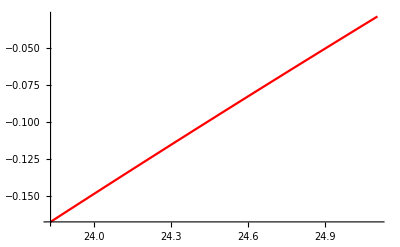

```mathematica
uSLplot=Plot[ UnitConvert[1/(β e)ySL[x*Quantity[10^(-10),"Meters"]/a],"SIBase"],{x,23.83,23.83+nuδCL},PlotStyle->Red]
```

## DL

#### dimensionless

```mathematica
yDL[x]
```

-76.0925 BesselK[0,3.55864 x]

#### plots with dimensions

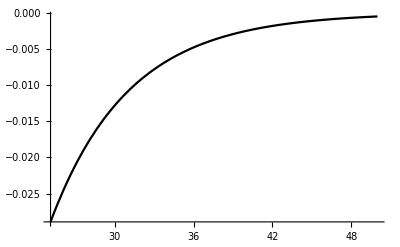

```mathematica
uDLplot=Plot[{UnitConvert[1/(β e)yDL[x*Quantity[10^(-10),"Meters"]/a],"SIBase"]},{x,23.83+nuδCL,50},PlotRange->Full,PlotStyle->Black,PlotLegends->"Expressions"]
```

```mathematica
UnitConvert[UnitConvert[1/(β e)yDL[(23.83+1.1012732237538216)*Quantity[10^(-10),"Meters"]/a],"SIBase"],"Volts"]
```

-0.0297728 V

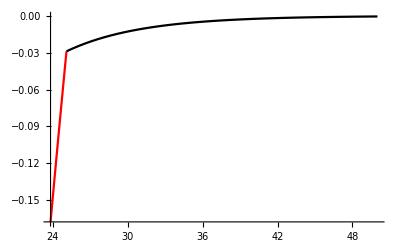

```mathematica
Show[uSLplot,uDLplot,PlotRange->All]
```

## 3. BDL vs “f”

eqn 44

```mathematica
fpH7 = 1-2/(1+√(1+√((-p/Log[δ])^2+1)))
```

0.460192

eqn 45 - NLDH

```mathematica
fc1pH7 = 1-4/(2+√(Abs[BDL]^2+4))
```

0.533425

eqn 46 - NLDH

```mathematica
fc2pH7 = 1-4/(2+√((Abs[BDL]*ArcSinh[BDL/2])^2+4))
```

0.710367

eqn 47 - Manning

```mathematica
fMpH7 = 1-2/Abs[BDL]
```

0.680585

## 4. Current

Transversal (Axial) Current

## SL

```mathematica
ΔVSLt=Vo
currRadial=CurrentTransSL
```

0.15

-16890.1 statC/(s statV)

```mathematica
(*currRadial=CurrentTransSL/.ΔVSLt->Vo*)
```

#### CGS

```mathematica
currRadial*UnitConvert[uVo,"StatVolts"]
```

-8.45091 statC/s

```mathematica
ItSLcgs =UnitConvert[currRadial*UnitConvert[uVo,"StatVolts"],"StatAmperes"]
```

-8.45091 statA

#### SI

```mathematica
ItSLsi =UnitConvert[ UnitSimplify[currRadial]*uVo,"Amperes"]
```

-2.81892×10^-9 A

## DL

```mathematica
ΔVDLt=Vo
```

0.15

```mathematica
CurrentTransDL
```

86997.8 statC/(s statV)

#### CGS

```mathematica
UnitConvert[CurrentTransDL,"Seconds"*"StatCoulombs"^2/("Grams"*"Centimeters"^2)]*UnitConvert[uVo,"StatVolts"]
```

43.529 s statC^2 statV/(g cm^2)

```mathematica
ItDLcgs =UnitConvert[ UnitSimplify[CurrentTransDL]*uVo,"StatAmperes"]
```

43.529 statA

#### SI

```mathematica
ItDLsi =UnitConvert[ UnitSimplify[CurrentTransDL]*uVo,"Amperes"]
```

1.45197×10^-8 A

Longitudinal (Axial) Current

## SL

```mathematica
ΔVSLl=Vo
ilSL=IlSL
```

0.15

9.42664 statC/(s statV)

```mathematica
(*ilSL=IlSL/.ΔVSLl->Vo*)
```

```mathematica
(*IlSL=ilSL/.ΔV->Vo*)
```

```mathematica
ilSL*uVo
```

0.00471658 statC/s

#### CGS

```mathematica
UnitConvert[ilSL,"Seconds"*"StatCoulombs"^2/("Grams"*"Centimeters"^2)]*UnitConvert[uVo,"StatVolts"]
```

0.00471658 s statC^2 statV/(g cm^2)

```mathematica
Ilslcgs=UnitConvert[ilSL*uVo,"StatAmperes"]
```

0.00471658 statA

```mathematica
UnitConvert[IlcSL (Quantity[0.05, "Volts"]),"StatAmperes"]
```

UnitConvert[IlcSL (0.05 V),StatAmperes]

#### SI

```mathematica
Ilslsi=UnitConvert[ilSL*uVo,"Amperes"]
```

1.57328×10^-12 A

## DL

```mathematica
ΔVDLl=Vo
ilDL=IlDL*uVo
```

0.15

0.360388 statC/s

```mathematica
(*ilDL=IlDL*uVo/.ΔVDLl->Vo*)
```

#### CGS

```mathematica
IlDLcgs=UnitConvert[ilDL,"StatAmperes"]
```

0.360388 statA

#### SI

```mathematica
IlDLsi=UnitConvert[ilDL,"Amperes"]
```

1.20212×10^-10 A

## 5. Resistance

Transversal (Axial) Resistance

## SL

```mathematica
RtSL
```

-8.88093×10^-6 s statV/statC

```mathematica
RtSLsi=UnitConvert[RtSL,"Ohms"]
```

-7.98178×10^6 Ω

```mathematica
uRtSLsi=Abs[RtSLsi]
```

7.98178×10^6 Ω

## DL

```mathematica
RtDL
```

4.1619×10^-6 s statV/statC

```mathematica
RtDLsi=UnitConvert[RtDL,"Ohms"]
```

3.74053×10^6 Ω

```mathematica
uRtDLsi=RtDLsi
```

3.74053×10^6 Ω

```mathematica
(*PathforMacBox - /Users/hunleyc/Desktop/00_Research/00_OtherFolders/00_JACFC_Results/Intracellular/postInflux/inputVoltage_0p15V/082120/preInflux_cCaEQ50nM/08-21-2020__20-24-35_simulationresults*)
(*uRtDLsi=Quantity[0.524*10^7,"Ohms"]*)
```

```mathematica
1.0868426051953934*^7/(4.74*10^6)
```

2.29292

## Equivalent Resistance

```mathematica
uRtEqsi =uRtDLsi +uRtSLsi
```

1.17223×10^7 Ω

Longitudinal (Axial) Resistance

## SL

```mathematica
RlSL
```

0.0159123 s statV/statC

```mathematica
RlSLsi=UnitConvert[RlSL,"Ohms"]
```

1.43013×10^10 Ω

```mathematica
uRlSLsi=RlSLsi
```

1.43013×10^10 Ω

## DL

```mathematica
RlDL
```

0.000208253 s statV/statC

```mathematica
RlDLsi=UnitConvert[RlDL,"Ohms"]
```

1.87169×10^8 Ω

```mathematica
uRlDLsi=RlDLsi
```

1.87169×10^8 Ω

```mathematica
(*PathforMacBox - /Users/hunleyc/Desktop/00_Research/00_OtherFolders/00_JACFC_Results/Intracellular/postInflux/inputVoltage_0p15V/082120/preInflux_cCaEQ50nM/08-21-2020__20-24-35_simulationresults*)
(*uRlDLsi=Quantity[0.199*10^9,"Ohms"]*)
```

```mathematica
1.7434096079950902*^8/(195*10^6)
```

0.894056

## Equivalent Resistance

```mathematica
uRlEqsi = uRlDLsi*uRlSLsi /(uRlDLsi+uRlSLsi)
```

1.84751×10^8 Ω

## 6. Capacitance

## SL

### q, L, M, NN terms

```mathematica
ζv =2*δ √(1/(3+δ^2))
```

0.908299

#### for q

```mathematica
(*BSL=*)4 π lBSL zp a σo/eo*(1/(4 π ϵo))
```

-1.83611×10^23 kg m^2 statC/(s^4 A^2 erg)

```mathematica
(*p =*) BSL/(2 εSL)δ
```

-9.78512

```mathematica
(*ζζ =√(ζ^2+(9 (1-δ^2)δ^2 p^2)/(5(3+δ^2)^3))*)
```

```mathematica
(*q =*)√(Expand[ζζ^2 p^2]+1)
```

√(1+0.603334 ζζ^2)

#### check q

```mathematica
(*α=(9 δ^2 (1-δ^2))/(5 (3+δ^2)^3)*)
```

```mathematica
γSL=UnitConvert[(2 a lBSL π zp δ)/(eo εSL)*(1/(4 π ϵo)),"Meters"^2/"Coulombs"]
```

250.702 m^2/C

```mathematica
(*p=γ σo*)
```

```mathematica
(*q=√(Expand[(γ^2 ζ^2 +α γ^4 σo^2)σo^2]+1)*)
```

#### L, M, NN in SI

```mathematica
L=UnitSimplify[1/(8 eo zp β)εSL^2 (-1+xcεDL^2 (1-2 Log[xcεDL]))]
```

-0.000305867 V

```mathematica
M=UnitSimplify[(4 a π xcεDL Log[xcεDL])/ϵSL(1/(4 π ϵo))]
```

2.95707 m V^2/N

```mathematica
NN=UnitSimplify[(8 a π BesselK[0,xcεDL εDL])/(ϵDL εDL BesselK[1,εDL])(1/(4 π ϵo))]
```

1.37445 m V^2/N

#### a check with SI units for L, M, NN

```mathematica
(*LSI =UnitSimplify[ (εSLSI^2 (-1+xcεDL^2 (1-2 Log[xcεDL])))/(8 eoSI zp βSI)]*)
```

```mathematica
(*MSI=UnitSimplify[(4 aSI π xcεDL Log[xcεDL])/ϵSL(1/(4 π ϵo))]*)
```

```mathematica
(*NNSI=UnitSimplify[(8 aSI π BesselK[0,xcεDL εDL])/(ϵDL εDLSI BesselK[1,εDL])(1/(4 π ϵo))]*)
```

### constants a0, a1, a2, a3

```mathematica
UnitConvert[a0SL,"Coulombs"/"Meters"^2]
```

0.0000839317 C/m^2

```mathematica
UnitConvert[a1SL,"Coulombs"/"Meters"^2/"Volts"]
```

0.274416 C/(m^2 V)

```mathematica
UnitConvert[a2SL,"Coulombs"/"Meters"^2/"Volts"^2]
```

0.0463456 C/(m^2 V^2)

```mathematica
UnitConvert[a3SL,"Coulombs"/"Meters"^2/"Volts"^3]
```

50.5075 C/(m^2 V^3)

### bSL

```mathematica
bSL
```

-0.168888 /V

```mathematica
bSLsi= UnitConvert[bSL,"Volts"]
```

-0.168888 /V

```mathematica
ubSLsi=bSLsi
```

-0.168888 /V

```mathematica
bSLVoEQ0p15VepsiEQ5cCa1mM=ubSLsi
```

-0.168888 /V

### CoSL

```mathematica
Coslsi=UnitConvert[a1SL,"Farads"/"Meters"^2]
```

0.274416 F/m^2

```mathematica
CoSLsi = UnitConvert[2*Pi*l*a*Coslsi,"Farads"]
```

2.21874×10^-17 F

```mathematica
uCoSLsi=CoSLsi
```

2.21874×10^-17 F

```mathematica
CoSLVoEQ0p15VepsiEQ5cCa1mM=uCoSLsi
```

2.21874×10^-17 F

## DL

### q, A, W terms

#### check q

```mathematica
(*ζv =2*δ √(1/(3+δ^2))*)
```

```mathematica
(*(2 a lBDL π zp δ)/(eo εDL)*)
```

```mathematica
(*γDL=UnitConvert[(2 a lBDL π zp δ)/(eo εDL)*(1/(4 π ϵo)),"Meters"^2/"Coulombs"]*)
```

#### A, W

```mathematica
(*A = UnitConvert[(8 a π BesselK[0,xc εDL])/(ϵDL εDL BesselK[1,εDL]),"SIBase"]*)
```

```mathematica
(*W=UnitConvert[A/(4 π ϵo),"Volts"*"Meters"^2/"Coulombs"]*)
```

#### a check with SI units for L, M, NN

```mathematica
(*LSI =UnitSimplify[ (εSLSI^2 (-1+xcεDL^2 (1-2 Log[xcεDL])))/(8 eoSI zp βSI)]*)
```

```mathematica
(*MSI=UnitSimplify[(4 aSI π xcεDL Log[xcεDL])/ϵSL(1/(4 π ϵo))]*)
```

```mathematica
(*NNSI=UnitSimplify[(8 aSI π BesselK[0,xcεDL εDL])/(ϵDL εDLSI BesselK[1,εDL])(1/(4 π ϵo))]*)
```

### constants a0, a1, a2, a3

```mathematica
(*a0DL*)
```

```mathematica
(*UnitConvert[a1DL,"Coulombs"/"Meters"^2/"Volts"]*)
```

```mathematica
(*a2DL*)
```

```mathematica
(*a3DL*)
```

```mathematica
(*UnitConvert[a3DL,"Coulombs"/"Meters"^2/"Volts"^3]*)
```

### bDL

```mathematica
(*ubDLsi=bDL*)
```

```mathematica
(*PathforMacBox - /Users/hunleyc/Desktop/00_Research/00_OtherFolders/00_JACFC_Results/Intracellular/postInflux/inputVoltage_0p15V/082120/preInflux_cCaEQ50nM/08-21-2020__20-24-35_simulationresults*)
```

```mathematica
ubDLsi=-1/2 Quantity[1.6478320175822678,1/"Volts"]
```

-0.823916 /V

```mathematica
bDL= ubDLsi
```

-0.823916 /V

```mathematica
bDLVoEQ0p15VepsiEQ5cCa1mM=ubDLsi
```

-0.823916 /V

### CoDL

```mathematica
(*Codlsi = UnitConvert[a1DL,"Farads"/"Meters"^2]*)
```

```mathematica
(*CoDLsi=UnitConvert[2*Pi*l*a*Codlsi,"Farads"]*)
```

```mathematica
(*uCoDLsi=CoDLsi*)
```

```mathematica
(*PathforMacBox - /Users/hunleyc/Desktop/00_Research/00_OtherFolders/00_JACFC_Results/Intracellular/preInflux/NaKCa_ClHPO4m2/07-30-2020__04-53-52_simulationresults*)
```

```mathematica
CoDLsi=Quantity[0.81289276761889040*2*π*(23.83*10^(-10))*(5.4*10^(-9)),"Farads"]
```

6.57251×10^-17 F

```mathematica
uCoDLsi=CoDLsi
```

6.57251×10^-17 F

```mathematica
CoDLVoEQ0p15VepsiEQ5cCa1mM=uCoDLsi
```

6.57251×10^-17 F

## Equivalent Capacitance and b parameter

### b parameter

```mathematica
btsi=(bSL  CoDLsi+bDL  CoSLsi)/(CoSLsi+CoDLsi)
```

-0.334205 /V

```mathematica
btsi
```

-0.334205 /V

```mathematica
ubtsi=btsi
```

-0.334205 /V

```mathematica
(*ubtsi=0.4489584775618532(*b parameter from SP1*)*)
```

```mathematica
0.4489584775618532
```

0.448958

```mathematica
(*PathforMacPro - /Users/chris/Desktop/Research/Research/00_OtherFolders/00_JACFC_Results/Divalent_Results/CaCl_KCl/pH7/cCaEQ0p005M/07-08-2020__18-03-51_simulationresults*)
(*ubtsi=Quantity[3.2381738940483373,1/"Volts"]*)
```

### Capacitance

```mathematica
uCoEqsi = (uCoSLsi*uCoDLsi)/(uCoSLsi+uCoDLsi)
```

1.65877×10^-17 F

```mathematica
(*PathforMacPro - /Users/chris/Desktop/Research/Research/00_OtherFolders/00_JACFC_Results/Divalent_Results/CaCl_KCl/pH7/cCaEQ0p005M/07-08-2020__18-03-51_simulationresults*)
(*uCoEqsi =Quantity[0.85545751961533945*2*π*(23.83*10^(-10))*(5.4*10^(-9)),"Farads"]*)
```

## 8. Self Inductance

## SL:

```mathematica
LSL
```

0

```mathematica
LSLsi=LSL
```

0

## DL:

```mathematica
LDL
```

0

```mathematica
LDLsi=LDL
```

0

## Equivalent:

```mathematica
LEq
```

0

#### CGS

```mathematica
LEqcgs=LEq
```

0

#### SI

```mathematica
LEqsi=LEq
```

0

## 8. Clear Parameters

### Clear Units

```mathematica
nuVo=QuantityMagnitude[uVo]
```

0.15

```mathematica
nul =QuantityMagnitude[l]
```

5.4×10^-9

#### Total

```mathematica
nuRtEq =QuantityMagnitude[uRtEqsi ]
```

1.17223×10^7

```mathematica
(*nuRtEq=4.748252092201714*^6*)
```

```mathematica
nuRlEq =QuantityMagnitude[uRlEqsi ]
```

1.84751×10^8

```mathematica
nuRtEq/nuRlEq
```

0.0634493

```mathematica
(*nuRlEq=195.0272920991057128*^6*)
```

```mathematica
(*MM: added this*)
```

```mathematica
(*nuZe=QuantityMagnitude[uZesi ]*)
```

```mathematica
(*nuZe=4.8972506598688365*^9*)
```

```mathematica
(*MM: added this*)
```

```mathematica
(*Vo=QuantityMagnitude[uVo]*)
```

```mathematica
(*MM: this parameter is negative*)
```

```mathematica
nubt=QuantityMagnitude[ubtsi]
```

-0.334205

```mathematica
(*nubt=0.47*)
```

```mathematica
nuCoEq=QuantityMagnitude[uCoEqsi]
```

1.65877×10^-17

```mathematica
(*l =5.4*10^(-10)*)
```

```mathematica
(*μ3 =(24 RlEq)/Ze*)
```

```mathematica
(*μ2 =(6 RtEq)/Ze*)
```

## 9. Impedance

### NEW IMPEDANCE ( newImpead )

```mathematica
Impedance=Sqrt[32/225 (25 π^4 nuRlEq^2+80 nubt π^4 nuRlEq nuRtEq nuVo+64 nubt^2 π^4 nuRtEq^2 nuVo^2)+8/225 √(-5625 π^4 nuRlEq^4+10000 π^8 nuRlEq^4-11250 π^4 nuRlEq^3 nuRtEq-5625 π^4 nuRlEq^2 nuRtEq^2-18000 nubt π^4 nuRlEq^3 nuRtEq nuVo+64000 nubt π^8 nuRlEq^3 nuRtEq nuVo-36000 nubt π^4 nuRlEq^2 nuRtEq^2 nuVo-18000 nubt π^4 nuRlEq nuRtEq^3 nuVo-14400 nubt^2 π^4 nuRlEq^2 nuRtEq^2 nuVo^2+153600 nubt^2 π^8 nuRlEq^2 nuRtEq^2 nuVo^2-28800 nubt^2 π^4 nuRlEq nuRtEq^3 nuVo^2-14400 nubt^2 π^4 nuRtEq^4 nuVo^2+163840 nubt^3 π^8 nuRlEq nuRtEq^3 nuVo^3+65536 nubt^4 π^8 nuRtEq^4 nuVo^4)];
```

```mathematica
nuZe= Impedance
```

4.8337×10^9

## Soliton

### KdV equation and more parameters Here we . . - solve for soliton

#### gamma

```mathematica
(*propagation of electrical impulse along actin filaments*)
(*alfa=(L/Ze+Co*Ze)*)

gamma=3*(LEq/nuZe+nuCoEq*nuZe)/(nubt*nuZe^(3/2)*nuCoEq);
```

#### μ2

```mathematica
μ2=nuRtEq*6/nuZe
```

0.0145507

#### μ3

```mathematica
μ3=nuRlEq*24/nuZe
```

0.917313

#### wo

```mathematica
(*      (*max possible value is 4.8*) (*Subscript[Ω, o] in equation 12 from Cameroon Paper*)*)
(* MM: I used the expression from our paper*)
```

```mathematica
wo=(nuVo*12/(Abs[gamma]*nuZe^(1/2)))^(1/2)
```

0.447798

#### alfa

```mathematica
alfa=(LEq/nuZe+nuCoEq*nuZe)
```

8.01802×10^-8

#### beta

```mathematica
beta=2*nul;
```

#### Ω

```mathematica
(*cwq=1/Sqrt[LEq*CEq];*)
```

```mathematica
Ω[τ1_]:=√((wo^2 ⅇ^(-(4 τ1 μ3)/3))/(1+((4 μ2  wo^2)/(5μ3))(1-ⅇ^(-(4 τ1 μ3)/3))));
```

#### ηe

```mathematica
(*MM: I changed from eta to etae. from some reason eta is protected....*)
```

```mathematica
ηe[τ1_] := -((5 (4 μ3 τ1+3 Log[5 μ3]-3 Log[-4 wo^2 μ2+ⅇ^((4 μ3 τ1)/3) (4 wo^2 μ2+5 μ3)]))/(4 μ2));
```

#### cW

```mathematica
cW[psi_,taoprima_]:=-2*(Ω[taoprima])^2*(Sech[Ω[taoprima]*(psi-ηe[taoprima])])^2;
```

#### velocityprop

```mathematica
(*MM: from our paper*)
```

```mathematica
(*velocityprop2[t_]:=4*wo^2* ⅇ^((-4 t μ3)/3)/(1+((4 μ2  wo^2)/(5μ3))(1-ⅇ^(-(4 t μ3)/3)));*)
```

```mathematica
velocityprop[t_]:=-1/(4 μ2)5 (4 μ3-(4 ⅇ^((4 t μ3)/3) μ3 (4 wo^2 μ2+5 μ3))/(-4 wo^2 μ2+ⅇ^((4 t μ3)/3) (4 wo^2 μ2+5 μ3)));
```

#### decaytime

```mathematica
decaytime=w/. Solve[Ω[w]==0.1*Ω[0],w][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

3.76315

```mathematica
(velocityprop[0]/24+1)/alfa*beta
```

0.139198

#### vavg

```mathematica
vavg = Integrate[(velocityprop[t/alfa/24]/24+1)/alfa*beta,{t,0,24*decaytime*alfa}]/(24*decaytime*alfa)
```

0.135664

```mathematica
avgVelocityVoEQ0p15VepsiEQ5cCaEQ1mM=vavg
```

0.135664

#### tmax

```mathematica
te=24*decaytime*alfa
tmax=te;
```

7.24153×10^-6

```mathematica
tmaxVoEQ0p15VϵSLEQ05cCaEQ1mM=7.241527043387776*^-6
```

7.24153×10^-6

#### xmax

```mathematica
xe=Abs[(1-te/alfa)*beta]*(1*10^6)
xmax=xe;
```

0.964609

```mathematica
xmaxVoEQ0p15VϵSLEQ05cCaEQ1mM=xmax
```

0.964609

#### velo

```mathematica
velo=xe/te*(1*10^-6)
```

0.133205

```mathematica
velocityVoEQ0p15VepsiEQ5cCaEQ1mM=velo
```

0.133205

#### Wx

```mathematica
(* with Dimensions *)
```

```mathematica
Wx[x_,t_]:=-2*(Ω[t/alfa/24])^2*(Sech[Ω[t/alfa/24]*((x/beta-t/alfa)-ηe[t/alfa/24])])^2
```

```mathematica
Wx[x,t]
```

-((0.401046 ⅇ^(-635592. t) Sech[0.447798 √(ⅇ^(-635592. t)/(1+0.00254461 (1-ⅇ^(-635592. t)))) (-1.24719×10^7 t+9.25926×10^7 x+85.9064 (4.5694+1.90678×10^6 t-3 Log[-0.011671+4.59824 ⅇ^(635592. t)]))]^2)/(1+0.00254461 (1-ⅇ^(-635592. t))))

#### Snapshot times for Soliton Plot

```mathematica
0
24*decaytime*alfa/10
24*decaytime*alfa/5
24*decaytime*alfa/3
24*decaytime*alfa/2
24*decaytime*alfa
```

0

7.24153×10^-7

1.44831×10^-6

2.41384×10^-6

3.62076×10^-6

7.24153×10^-6

Plots

### Velocity plots

#### Total

Intracellular conditions

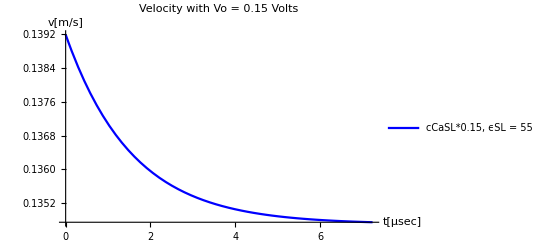

```mathematica
Print["Intracellular conditions"]

veloSP2=Plot[(velocityprop[t/alfa/24*10^-6]/24+1)/alfa*beta,{t,0,24*decaytime*alfa*10^6},PlotLegends->{"cCaSL*0.15, ϵSL = 55"},PlotLabel->"Velocity with Vo = 0.15 Volts",PlotStyle->Blue,PlotRange->Full,Axes->True,AxesLabel->{"t[μsec]","v[m/s]"}]
```

```mathematica
24*0.329*3.6
```

28.4256

```mathematica
veloSP2Data=Cases[veloSP2,Line[{x__}]->x,∞];
```

### Soliton Peak Attenuation plots

```mathematica
(*MM: added ABS[] and divided by 24, not 12*)
```

#### Total

Intracellular conditions

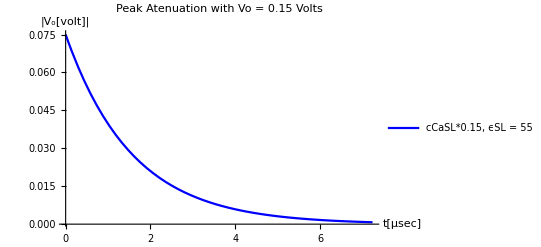

```mathematica
Print["Intracellular conditions"]

peakDecaySP2wSP1Capa=Plot[{Abs[Ω[t/alfa/24*10^-6]^2*gamma*nuZe^(1/2)/24]},{t,0,24*decaytime*alfa*10^6},PlotStyle->Blue,PlotLegends->{"cCaSL*0.15, ϵSL = 55"},PlotLabel->"Peak Atenuation with Vo = 0.15 Volts",Axes->True,AxesLabel->{"t[μsec]","|V_o[volt]|"},PlotRange->All]
```

```mathematica
peakDecaySP2wSP1CapaData=Cases[peakDecaySP2wSP1Capa,Line[{x__}]->x,∞];
```

Soliton Propagation plots

```mathematica
(*Vo=0.15V ϵSL = 78.358 cCa=50nM*)
tmaxVoEQ0p15VϵSLEQ78p358cCaEQ50nM=0.000016722898823157003
```

0.0000167229

```mathematica
(*Vo=0.05V ϵSL = 78.358 cCa=50nM*)
tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM=0.000016787268912085657
```

0.0000167873

```mathematica
tmaxThisFile=24*decaytime*alfa
```

7.24153×10^-6

## Soliton Normalized

#### Normalized - regular

Intracellular conditions at 0.05 and 0.15 molar concentration: A normalized plot

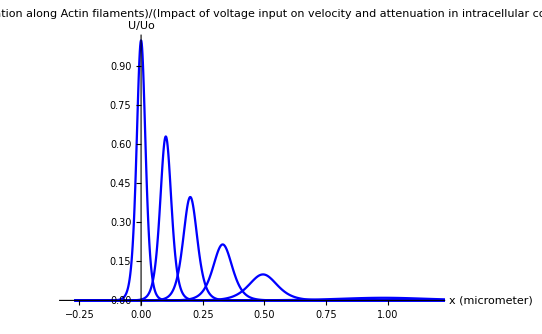

```mathematica
Print["Intracellular conditions at 0.05 and 0.15 molar concentration: A normalized plot"]

SolNormTot=Plot[ {-Wx[x*10^-6,0]/wo^2/2,
-Wx[x*10^-6,tmaxThisFile/10]/wo^2/2,
-Wx[x*10^-6,tmaxThisFile/5]/wo^2/2,
-Wx[x*10^-6,tmaxThisFile/3]/wo^2/2,
-Wx[x*10^-6,tmaxThisFile/2]/wo^2/2,
-Wx[x*10^-6,tmaxThisFile]/wo^2/2},{x,-25*beta*10^6,435*beta*10^6},PlotRange->{{-0.3,1.2},{0,1}},Axes->True,AxesLabel->{"x (micrometer)","U/Uo"},PlotLabel->Style["Soliton propagation along Actin filaments" /" in intracellular conditions" / "Impact of voltage input on velocity and attenuation",Black,FontSize->18,Bold],AxesStyle->Directive[Black,FontSize-> 18],TicksStyle->Directive[18],PlotStyle->{{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]}},PlotLegends->Placed[{},{0.87,0.6}],LabelStyle->{18}]
```

```mathematica
NormSolSP22Data=Cases[SolNormTot,Line[{x__}]->x,∞];
```

#### -- normalized compare with tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM

Intracellular conditions at 0.05 and 0.15 molar concentration: A normalized plot

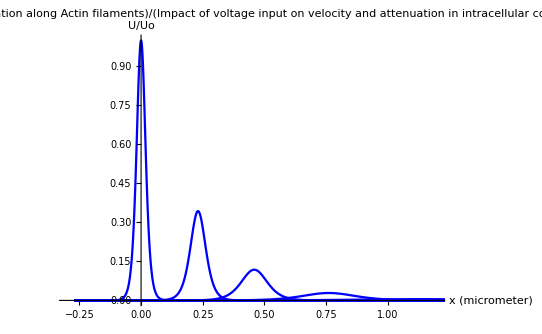

```mathematica
Print["Intracellular conditions at 0.05 and 0.15 molar concentration: A normalized plot"]

SolNormTot2=Plot[ {-Wx[x*10^-6,0]/wo^2/2,
-Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/10]/wo^2/2,
-Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/5]/wo^2/2,
-Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/3]/wo^2/2,
-Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/2]/wo^2/2,
-Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM]/wo^2/2},{x,-25*beta*10^6,435*beta*10^6},PlotRange->{{-0.3,1.2},{0,1}},Axes->True,AxesLabel->{"x (micrometer)","U/Uo"},PlotLabel->Style["Soliton propagation along Actin filaments" /" in intracellular conditions" / "Impact of voltage input on velocity and attenuation",Black,FontSize->18,Bold],AxesStyle->Directive[Black,FontSize-> 18],TicksStyle->Directive[18],PlotStyle->{{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]}},PlotLegends->Placed[{},{0.87,0.6}],LabelStyle->{18}]
```

```mathematica
NormSolSP22Data2=Cases[SolNormTot2,Line[{x__}]->x,∞];
```

## Soliton

#### regular Plot

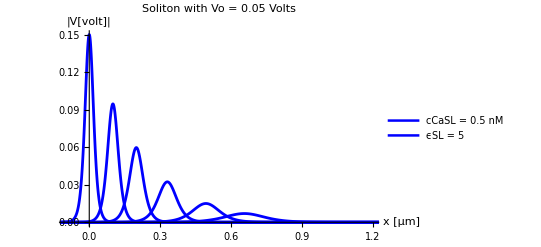

```mathematica
solSP22=Plot[ {Abs[Wx[x*10^-6,0]*gamma*nuZe^(1/2)/24],
Abs[Wx[x*10^-6,tmaxThisFile/10]*gamma*nuZe^(1/2)/24],Abs[Wx[x*10^-6,tmaxThisFile/5]*gamma*nuZe^(1/2)/24],Abs[Wx[x*10^-6,tmaxThisFile/3]*gamma*nuZe^(1/2)/24],
Abs[Wx[x*10^-6,tmaxThisFile/2]*gamma*nuZe^(1/2)/24],Abs[Wx[x*10^-6,tmaxThisFile/1.5]*gamma*nuZe^(1/2)/24]},
{x,-25*beta*10^6,120*beta*10^6},PlotRange->{{-0.1,1.2},{0,0.15}},PlotLegends->{"cCaSL = 0.5 nM", "ϵSL = 5"},PlotLabel->"Soliton with Vo = 0.05 Volts",Axes->True,AxesLabel->{"x [μm]","|V[volt]|"},AxesStyle->Directive[Black,FontSize-> 18],TicksStyle->Directive[18],PlotStyle->{{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]}},PlotLegends->Placed[{},{0.87,0.6}],LabelStyle->{18}]
```

```mathematica
solSP22Data=Cases[solSP22,Line[{x__}]->x,∞];
```

#### compare regular with tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM

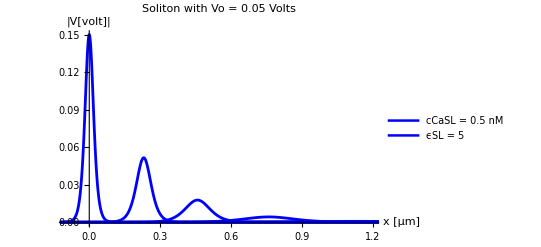

```mathematica
(*Print["Intracellular conditions at 0.05 and 0.15 molar concentration"]*)

solSP2=Plot[ {Abs[Wx[x*10^-6,0]*gamma*nuZe^(1/2)/24],
Abs[Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/10]*gamma*nuZe^(1/2)/24],Abs[Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/5]*gamma*nuZe^(1/2)/24],Abs[Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/3]*gamma*nuZe^(1/2)/24],
Abs[Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/2]*gamma*nuZe^(1/2)/24],Abs[Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/1.5]*gamma*nuZe^(1/2)/24]},
{x,-25*beta*10^6,120*beta*10^6},PlotRange->{{-0.1,1.2},{0,0.15}},PlotLegends->{"cCaSL = 0.5 nM", "ϵSL = 5"},PlotLabel->"Soliton with Vo = 0.05 Volts",Axes->True,AxesLabel->{"x [μm]","|V[volt]|"},AxesStyle->Directive[Black,FontSize-> 18],TicksStyle->Directive[18],PlotStyle->{{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]}},PlotLegends->Placed[{},{0.87,0.6}],LabelStyle->{18}]
```

```mathematica
solSP2Data=Cases[solSP2,Line[{x__}]->x,∞];
```